# Least Squares Solutions/Data Fitting (4/16/16)

Question:  Find the least squares solution to 
x + y = 1
x - 3y = 4
2x + y = 3.

```mathematica
(*Here are the matrices a, b*)
a = {{1,1},{1,-3},{2,1}};
b = {{1},{4},{3}};
MatrixForm[a]
MatrixForm[b]
```

(1 | 1
1 | -3
2 | 1)

(1
4
3)

```mathematica
(*Here are two ways of obtaining the transpose.*)
Transpose[a] // MatrixForm
aᵀ // MatrixForm
```

(1 | 1 | 2
1 | -3 | 1)

(1 | 1 | 2
1 | -3 | 1)

```mathematica
(soln = Inverse[Transpose[a].a].Transpose[a].b ) // MatrixForm
```

(11/6
-8/11)

The least squares solution is y = (11/6)x - 8/11.

```mathematica
N[a.soln]
```

{{1.10606},{4.01515},{2.93939}}

Note that the output values obtained from our solution are very close to the values of b in the original problem.

Question: Find the line y=ax + b that best fits the data (-1,1), (1,2), (2,-1).

```mathematica
a = {{-1,1},{1,1},{2,1}};
MatrixForm[a]
b = {1,2,-1};
MatrixForm[b]
```

(-1 | 1
1 | 1
2 | 1)

(1
2
-1)

```mathematica
Inverse[Transpose[a].a].Transpose[a].b  // MatrixForm
```

(-1/2
1)

The line y = -1/2 x + 1 is the best fit line.

Question: Find the parabola that best fits the data points (-1,8), (0,8), (1,4), (2, 16).

Here, I will illustrate how Mathematica has built-in commmands for the methods we are using.

```mathematica
data = {{-1,8},{0,8},{1,4},{2,16}};
MatrixForm[data]
```

(-1 | 8
0 | 8
1 | 4
2 | 16)

```mathematica
quad = Fit[data, {1, x, x^2}, x]
```

5.-1. x+3. x^2

The parabola that best fits the data is 3x^2 - x + 5.  Here is a graph with the data points and the quadratic function.

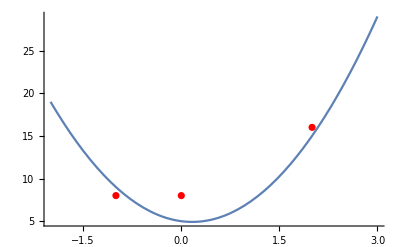

```mathematica
Show[Plot[quad, {x, -2, 3}], ListPlot[data, PlotStyle -> Red]]
```

Note that we can find a cubic function going through all 4 data points.

8.-5.33333 x-2. x^2+3.33333 x^3

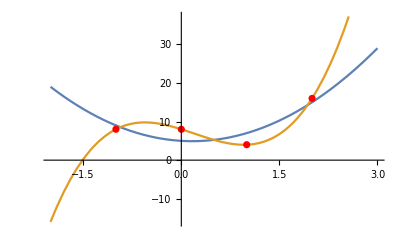

```mathematica
cubic = Fit[data, {x^3,x^2, x, 1}, x]
Show[Plot[{quad, cubic}, {x, -2, 3}], ListPlot[data, PlotStyle -> Red]]
```

Finally, here are some tricks for producing and manipulating matrices.

To access the (i,j)th entry in a matrix, you use [[i,j]].  For example, the various entries of data can be accessed as follows.

```mathematica
(data = {{-1,8},{0,8},{1,4},{2,16}})// MatrixForm
data[[2,2]] (*Row 2, Column 2*)
data[[3,1]] (*Row 3, Column 1*)
data[[3,3]]  (*Row 3, Column 3, which does not exist*)
```

(-1 | 8
0 | 8
1 | 4
2 | 16)

8

1

Part::partw: Part 3 of {1,4} does not exist.

{{-1,8},{0,8},{1,4},{2,16}}⟦3,3⟧

Here is a way we can use the data table to create matrices a, b.

```mathematica
(xvals = Table[data[[i,1]], {i, 1, 4}]) 
(b = Table[data[[i,2]], {i, 1, 4}]) // MatrixForm
(a =Table[ { i^2, i, 1}  , {i, xvals}]) // MatrixForm
```

{-1,0,1,2}

(8
8
4
16)

(1 | -1 | 1
0 | 0 | 1
1 | 1 | 1
4 | 2 | 1)

```mathematica
Inverse[Transpose[a].a].Transpose[a].b  // MatrixForm
```

(3
-1
5)

or, there is a built-in command for LeastSquares.

```mathematica
LeastSquares[a,b]
```

{3,-1,5}

If you are interested in Problem 5:  Here is an example of creating a list of (x,y) values for the curve y = x^2 - 1, from x=1 to x=3, with step size of 1/5.

```mathematica
Table[{x, x^2-1}, {x, 1, 3, .2}]
```

{{1.,0.},{1.2,0.44},{1.4,0.96},{1.6,1.56},{1.8,2.24},{2.,3.},{2.2,3.84},{2.4,4.76},{2.6,5.76},{2.8,6.84},{3.,8.}}

Here is an example of (x,y) values for y=sin(x), from x=1 to x=3 with step size of .2.

```mathematica
Table[{x, Sin[x]}, {x, 1, 3, .2}]
```

{{1.,0.841471},{1.2,0.932039},{1.4,0.98545},{1.6,0.999574},{1.8,0.973848},{2.,0.909297},{2.2,0.808496},{2.4,0.675463},{2.6,0.515501},{2.8,0.334988},{3.,0.14112}}